```mathematica
m1d=Import["/Users/benxgh1996/Desktop/Muon/muon_1.data","Table"]
```

{{40000,1518120833},{40000,1518120834},{40005,1518120835},{40003,1518120836},{40003,1518120837},{40000,1518120838},{40004,1518120839},{40002,1518120840},{40002,1518120841},{40003,1518120842},{40006,1518120843},{40009,1518120844},{40002,1518120845},{40000,1518120846},791077,{40008,1519934344},{40004,1519934345},{40005,1519934346},{40005,1519934347},{40003,1519934348},{40005,1519934349},{40006,1519934350},{40004,1519934351},{40004,1519934352},{40007,1519934353},{40005,1519934354},{40006,1519934355},{40000,1519934356}}
 |  |  |  |

```mathematica
(*Filtered data that only contains measurements of our first lab day *)
```

```mathematica
m1df=Select[m1d,#[[2]]>=1519770660&&#[[1]]<40000&]
```

{{40,1519770662},{100,1519770710},{40,1519770761},{40,1519770907},{40,1519770971},{40,1519771041},{540,1519771091},{40,1519771098},{40,1519771140},{2580,1519771157},{40,1519771218},{40,1519771225},{40,1519771266},{40,1519771303},{5160,1519771509},{40,1519771515},2737,{11320,1519933792},{40,1519933824},{40,1519933824},{40,1519933827},{40,1519933876},{3460,1519933981},{40,1519934000},{40,1519934075},{40,1519934077},{820,1519934095},{40,1519934124},{40,1519934167},{5200,1519934187},{40,1519934195},{40,1519934262},{4460,1519934333}}
 |  |  |  |

```mathematica
m1dt=#[[1]]&/@m1df
```

```mathematica
m1dtSort=Sort[m1dt]
```

```mathematica
Count[m1dt,u_/;u>60]
```

697

```mathematica
m1dtSort
```

```mathematica
m1dtLarge=Select[m1dtSort, #>100&]
```

```mathematica
m1Log300=getLogList[m1dtLarge,20,300]
```

{{320,Log[205]},{1235,Log[131]},{2150,Log[76]},{3065,Log[46]},{3980,Log[39]},{4895,Log[30]},{5810,Log[15]},{6725,Log[6]},{7640,Log[10]},{8555,Log[10]},{9470,Log[5]},{10385,Log[3]},{11300,Log[5]},{12215,Log[2]},{13130,0},{14045,Log[5]},{14960,Log[5]},{15875,0},{16790,Log[3]},{17705,0}}

```mathematica
Select[m1Log300,]
```

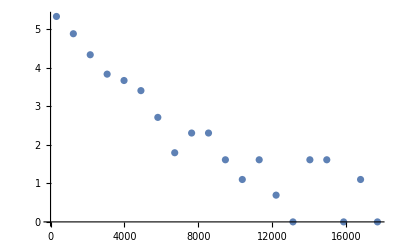

```mathematica
ListPlot[Tooltip[m1Log300],#[[1]]<=12215&]
```

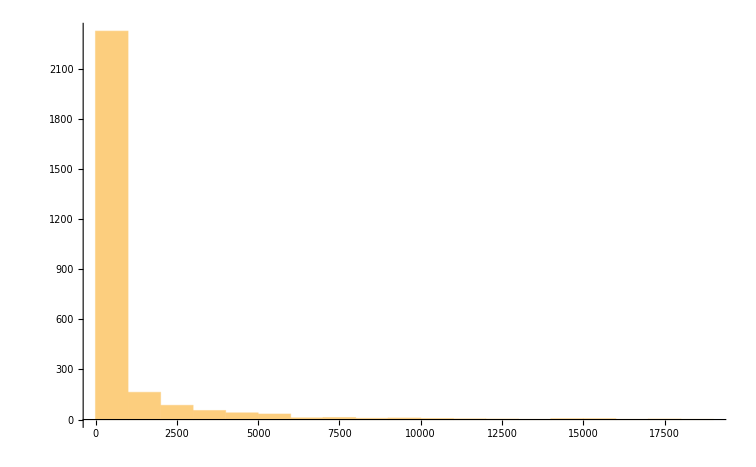

```mathematica
Histogram[m1dt,20]
```

```mathematica
Max[m1dtSort]
```

18600

```mathematica
Length[m1dtSort]
```

2769

```mathematica
(*data: the muon decay time data;
  numBin: the number of bins that you want to set up to prepare the muon decay distribution;*)
```

```mathematica
dat=m1dtSort;
```

```mathematica
Dimensions@dat
```

{2769}

```mathematica
distGet[d_,n_]:=Min@d+Range[0,n-1]Ceiling[(Max@d-Min@d+1)/n]
```

```mathematica
Min@#1+Range[0,#2-1]Ceiling[(Max@#1-Min@#1+1)/#2]&[dat,3]
```

```mathematica
f2[d_,n_]:=Length/@BinLists[d,{Min@d,Max@d+n,Ceiling[(Max@d-Min@d+1)/n]}]
```

```mathematica
BinLists[Range@10,{1,13,3}]
```

{{1,2,3},{4,5,6},{7,8,9},{10}}

```mathematica
f2[dat,6]
```

{2583,123,30,16,11,6}

```mathematica
ⅇ^{{1,2},{3,4}}
```

{{ⅇ,ⅇ^2},{ⅇ^3,ⅇ^4}}

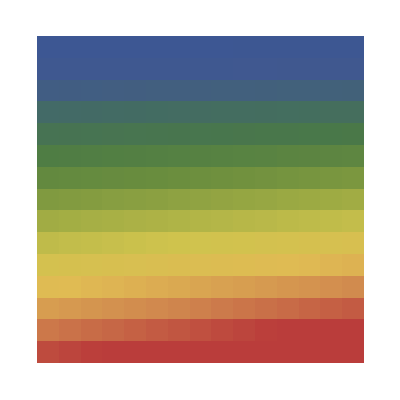

```mathematica
ArrayPlot[MatrixExp[Partition[Range@225,15]//N],ColorFunction->"DarkRainbow",Frame->False]
```

```mathematica
f@x
f[x]
x//f
```

```mathematica
f[x,y]
x~f~y
```

```mathematica
Sin[f2[dat,10]+1]
```

{Sin[2479],Sin[139],Sin[78],Sin[24],Sin[21],Sin[11],Sin[8],Sin[7],Sin[7],Sin[5]}

```mathematica
BarChart[f2[dat,i]+1,PlotRange->All,ColorFunction->"DarkRainbow",(*Joined->True,*)ScalingFunctions->"Log",Axes->False,Frame->True,FrameLabel->{"Times","Counts"},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed,Opacity@.15]]~Manipulate~{i,1,200,1}
```

```mathematica
Length@f2[dat,i]~Manipulate~{i,1,10,1}
```

```mathematica
Length/@f2[dat,3]
```

{0,0,0,0}

```mathematica
Total@{2705,46,17,1}
```

2769

```mathematica
Length@dat
```

2769

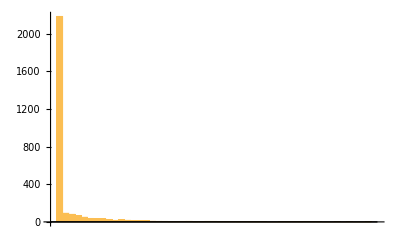

```mathematica
BarChart[Length/@f2[dat,50]]
```

```mathematica
SplitBy[dat,Min@#1+Range[0,#2-1]Ceiling[(Max@#1-Min@#1+1)/#2]&[dat,3]
```

```mathematica
SplitBy[Range@10,{#>3&,#>6&}]
```

{{{1,2,3}},{{4,5,6},{7,8,9,10}}}

```mathematica
getDist[dat,3]
```

{{{40,2706},{6227,46},{12414,17}},3,6187}

```mathematica
getDist[data_,numBin_]:=Module[
(*maxTime: the largest muon lifetime recorded;
  dist: a list that contains elements of {start_time, count};*)
{minTime,maxTime,t,i,binWidth,dataLen,dist,count},
(* specify the width of each bin. It should not matter that we set the width of each bin to be
slightly larger, i.e. to be the next integer. In this case, the total number of bins to cover
all the data should still be the same. *)
minTime=Min@data;
maxTime=Max@data;
(*Need to have maxTime+1 because the start time of the first bin is 0.*)
binWidth=Ceiling[(maxTime-minTime+1)/numBin];

(* Now we want to create our distribution list of the decay data in form of {start time of decay, number of decays in this bin} *)
dist={};
For[i=0,i≤(numBin-1),i++,
(*So basically each bin is an interval of [start_time, start_time + binWidth)*) 
t=minTime+i*binWidth;
count=Count[data,u_/;u≥t&&u<(t+binWidth)];
AppendTo[dist,{t,count}]
];
{dist, numBin, binWidth}
]
```

```mathematica
getDist[dat,3]
```

{{{40,2706},{6227,46},{12414,17}},3,6187}

```mathematica
HistogramList[dat,3]
```

{{0,10000,20000},{2740,29}}

```mathematica
getDist[m1dtSort,20]
```

{{{40,2322},{969,156},{1898,80},{2827,58},{3756,47},{4685,30},{5614,17},{6543,6},{7472,11},{8401,9},{9330,6},{10259,4},{11188,4},{12117,3},{13046,1},{13975,5},{14904,5},{15833,1},{16762,3},{17691,1}},20,929}

```mathematica
#[[2]]&/@%109[[1]]
```

{2322,156,80,58,47,30,17,6,11,9,6,4,4,3,1,5,5,1,3,1}

```mathematica
Total[%111]
```

2769

```mathematica
getLogList[data_,numBin_,thresh_]:=Module[
{dataThresh,dataDist,dataDistLog},
(*Subtracting the very first data points with small decay times.*)
dataThresh=Select[data,#>thresh&];

dataDist=getDist[dataThresh,numBin][[1]];
dataDistLog={#[[1]],Log@#[[2]]}&/@dataDist;
dataDistLog
]
```

```mathematica
list=Select[m1dtSort,#>300&]
```

```mathematica
Min[list]
```

320

```mathematica
getDist[list,20][[1]]
```

{}

```mathematica
getLogList[m1dtSort,20,300]
```

{}

```mathematica
getDist[m1dtSort,20][[1]]
```

{{0,2312},{931,164},{1862,76},{2793,63},{3724,48},{4655,30},{5586,17},{6517,6},{7448,11},{8379,8},{9310,7},{10241,4},{11172,4},{12103,3},{13034,1},{13965,5},{14896,5},{15827,1},{16758,3},{17689,1}}

```mathematica
(*This is the histogram distribution of data m1*)
```

```mathematica
m1Dist=getDist[m1dtSort,20][[1]]
```

{{0,2312},{931,164},{1862,76},{2793,63},{3724,48},{4655,30},{5586,17},{6517,6},{7448,11},{8379,8},{9310,7},{10241,4},{11172,4},{12103,3},{13034,1},{13965,5},{14896,5},{15827,1},{16758,3},{17689,1}}

```mathematica
#[[2]]&/@m1Dist
```

```mathematica
Total[{2312,164,76,63,48,30,17,6,11,8,7,4,4,3,1,5,5,1,3,1}]
```

2769

```mathematica
m1LogDist={#[[1]],Log@#[[2]]}&/@m1Dist
```

{{0,Log[2312]},{931,Log[164]},{1862,Log[76]},{2793,Log[63]},{3724,Log[48]},{4655,Log[30]},{5586,Log[17]},{6517,Log[6]},{7448,Log[11]},{8379,Log[8]},{9310,Log[7]},{10241,Log[4]},{11172,Log[4]},{12103,Log[3]},{13034,0},{13965,Log[5]},{14896,Log[5]},{15827,0},{16758,Log[3]},{17689,0}}

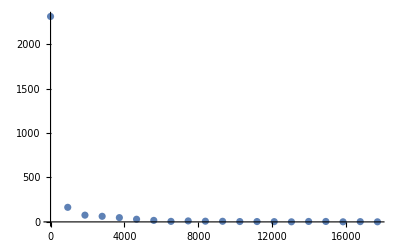

```mathematica
ListPlot[m1Dist,PlotRange->All]
```

```mathematica
nf=Nearest[m1LogDist];
```

```mathematica
ListPlot[m1LogDist,
Epilog->Dynamic@DynamicModule[{pt=nf[MousePosition[{"Graphics",Graphics},{0,0}]],scaled=MousePosition[{"GraphicsScaled",Graphics},None]},If[scaled===None,{},{Text[pt[[1]],pt[[1]],{1.5 Sign[scaled[[1]]-.5],0},Background-> White],AbsolutePointSize[7],Point[pt],Black,AbsolutePointSize[5],Point[pt]}]]]
```

-Graphics-

```mathematica
FindFit[m1LogDist,-λ x +b,{λ,b},x]
```

{λ→0.000311671,b→5.14802}

```mathematica
1/λ/.λ->0.0003116706209601906
```

3208.52

```mathematica
(*m1LogClear is m1LogDist that excludes data in the first channel and in the last channels*)
```

```mathematica
m1LogClear=Select[m1LogDist,(#[[1]]>931&&#[[1]]<13034)&]
```

{{1862,Log[76]},{2793,Log[63]},{3724,Log[48]},{4655,Log[30]},{5586,Log[17]},{6517,Log[6]},{7448,Log[11]},{8379,Log[8]},{9310,Log[7]},{10241,Log[4]},{11172,Log[4]},{12103,Log[3]}}

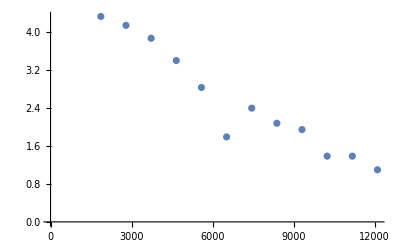

```mathematica
ListPlot[Tooltip[m1LogClear]]
```

```mathematica
FindFit[m1LogClear,-λ t+b,{λ,b},t]
```

{λ→0.00032558,b→4.82884}

```mathematica
1/λ/.λ->0.0003255798981858529
```

3071.44

```mathematica
m2d=Import["/Users/benxgh1996/Desktop/Muon/muon_2.data","Table"]
```

{{40000,1519943777},{40000,1519943778},{40003,1519943779},{40000,1519943780},{40001,1519943781},{40001,1519943782},{40000,1519943783},{40000,1519943784},{40000,1519943785},{40001,1519943786},{40001,1519943787},{40001,1519943788},{40000,1519943789},{40000,1519943790},422730,{40000,1520366317},{40000,1520366318},{40000,1520366319},{40000,1520366320},{40000,1520366321},{40000,1520366322},{40000,1520366323},{40000,1520366324},{40002,1520366325},{40003,1520366326},{40000,1520366327},{40000,1520366328},{40000,1520366329},{40000,1520366330}}
 |  |  |  |

```mathematica
m2df=Select[m2d,#[[1]]<40000&]
```

```mathematica
m2dt=#[[1]]&/@m2df
```

```mathematica
m2dtSort=Sort[m2dt]
```

{40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,120,120,120,120,120,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,160,160,160,160,160,160,160,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,220,220,220,220,220,220,220,220,220,220,220,240,240,240,240,240,240,240,240,240,240,240,240,240,240,280,280,280,280,280,280,280,280,280,280,280,300,300,300,300,300,300,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,340,340,340,340,340,340,340,340,340,340,340,340,340,340,340,360,360,360,360,360,360,360,360,360,360,380,380,380,380,380,380,380,380,380,380,380,380,380,380,380,380,380,380,380,380,380,380,380,380,380,380,380,380,380,380,380,420,420,460,460,480,480,480,480,500,520,520,520,520,520,520,520,520,520,520,520,560,560,560,560,560,560,560,560,560,560,560,560,600,600,600,600,620,620,620,620,640,660,660,660,660,660,660,660,660,680,680,680,700,700,700,700,700,700,700,700,700,700,700,720,740,760,760,780,780,800,800,840,840,840,840,840,840,840,840,840,860,860,860,860,860,880,880,900,900,900,900,920,940,940,940,940,960,960,960,980,980,980,980,980,980,980,1000,1020,1020,1020,1040,1040,1040,1040,1040,1060,1060,1080,1080,1080,1080,1100,1100,1120,1120,1140,1160,1180,1180,1180,1180,1180,1180,1180,1180,1180,1180,1180,1180,1200,1200,1220,1220,1220,1220,1220,1220,1220,1220,1220,1220,1220,1240,1240,1240,1260,1260,1260,1260,1280,1300,1300,1320,1320,1340,1340,1340,1360,1360,1400,1400,1400,1420,1460,1460,1460,1460,1480,1480,1500,1500,1500,1500,1500,1500,1500,1500,1540,1540,1540,1540,1560,1560,1580,1600,1620,1640,1640,1640,1640,1640,1660,1660,1680,1680,1700,1700,1700,1700,1700,1700,1720,1740,1740,1740,1780,1780,1780,1780,1820,1840,1840,1840,1860,1860,1880,1880,1880,1940,1980,1980,2000,2000,2000,2020,2020,2020,2020,2020,2020,2020,2020,2040,2040,2040,2040,2060,2060,2080,2080,2080,2100,2120,2120,2140,2160,2160,2160,2160,2180,2200,2200,2200,2200,2220,2220,2280,2300,2340,2360,2380,2380,2420,2420,2440,2540,2540,2540,2540,2580,2620,2640,2640,2640,2640,2680,2680,2680,2680,2720,2740,2760,2820,2820,2820,2840,2860,2880,2900,2920,2920,2960,3000,3000,3060,3060,3060,3100,3100,3120,3140,3140,3160,3180,3180,3220,3300,3320,3340,3340,3360,3380,3380,3380,3380,3380,3420,3440,3480,3500,3520,3540,3600,3700,3700,3720,3720,3760,3840,3860,3880,3880,3980,4000,4000,4040,4040,4060,4080,4200,4320,4320,4420,4420,4740,4900,4980,5020,5160,5220,5260,5280,5340,5360,5400,5400,5420,5540,5580,5580,5620,5860,5880,5980,5980,6100,6160,6200,6220,6340,6440,6480,6480,6520,6520,6720,6720,6780,7000,7100,7100,7240,7320,7340,7360,7420,7480,7660,7720,7800,7940,7940,7980,8080,8280,8540,8560,8560,8600,8700,8740,8880,8880,8920,8920,9020,9020,9060,9060,9120,9200,9260,9380,9500,9540,9580,9680,9720,9820,9860,9860,9960,10100,10240,10320,10320,10340,10380,10460,10480,10580,10620,10660,10660,10760,10860,11220,11460,11500,11560,12300,12680,12680,12960,12960,13180,13380,14240,14260,14780,15160,15620,16940,16940,17280,17520,18580,18600,18860,18880,19180,19200,19240,19500,19820}

```mathematica
Length[m2dt]
```

1299

```mathematica
Count[m2dt,u_/;u≤60]
```

460

```mathematica
1299-460
```

839

```mathematica
expo[τ_,x_]:=1/τ*ⅇ^(-x/τ)
```

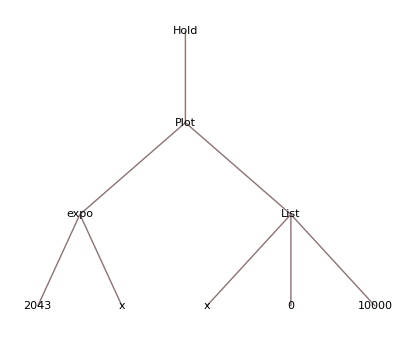

```mathematica
TreeForm@Hold[Plot[expo[2043,x],{x,0,10000}]]
```

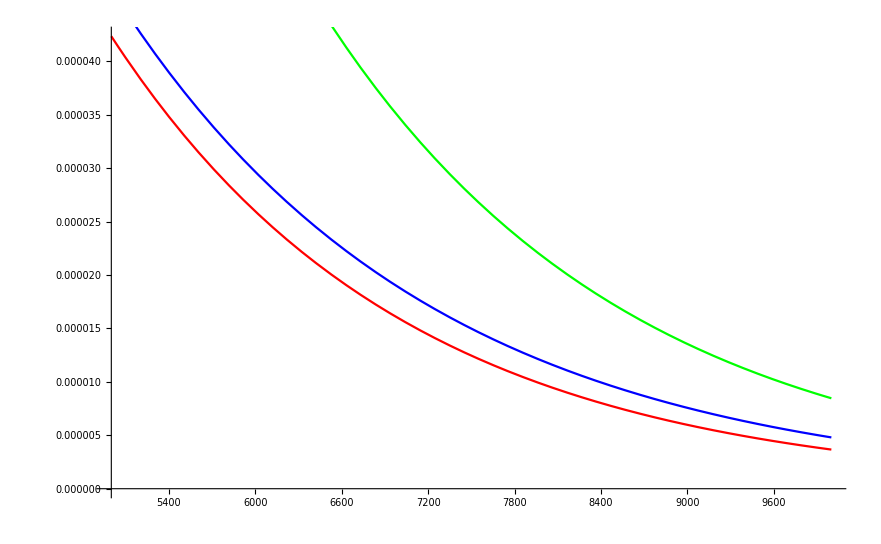

```mathematica
Show[Plot[expo[2043,x],{x,5000,10000},PlotStyle->Red],Plot[expo[2197,x],{x,5000,10000},PlotStyle->Blue],Plot[expo[2043,x]+expo[2197,x],{x,5000,10000},PlotStyle->Green]]
```

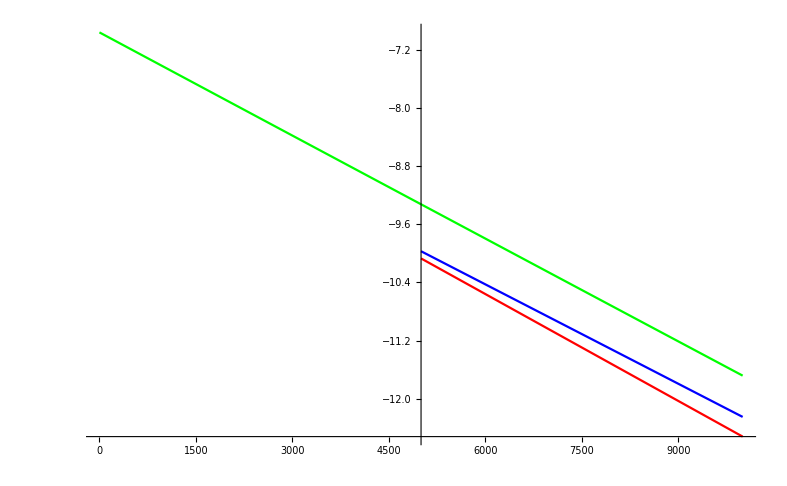

```mathematica
Show[Plot[Log[expo[2043,x]],{x,5000,10000},PlotStyle->Red],Plot[Log[expo[2197,x]],{x,5000,10000},PlotStyle->Blue],Plot[Log[expo[2043,x]+expo[2197,x]],{x,0,10000},PlotStyle->Green],PlotRange-> All]
```

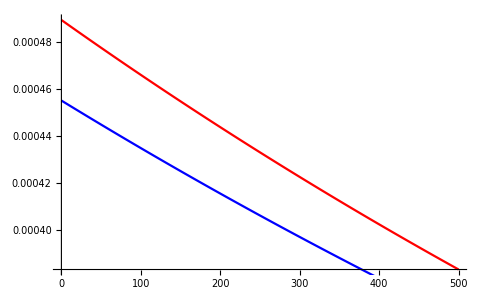

```mathematica
Show[Plot[expo[2043,x],{x,0,500},PlotStyle->Red],Plot[expo[2197,x],{x,0,500},PlotStyle->Blue]]
```